```mathematica
d=1*10^-3;
ρ=1333;
σ=0.0295;
σT=2.148*10^-4;
ΔT=10;
ν=3.477*10^-7;
Cp=1.18*10^3;
k=0.14;
χ=k/(ρ Cp);
g=0;
L1=350*10^3;
Print["G"]
G1=g d^3/(ν χ)
Print["M"]
M1=σT ΔT d/(ρ ν χ)
Print["S"]
S1=(σ d)/(3 ρ ν^2)
Bo=G1/S1;
K1=1;
B=0.0;
Bi=1+B K;
P1=ν/χ;
A1=1.987*10^-11;
a=A1/S1;
m=(M1 K1 Bi)/(2 P1 S1)
Print["E"]
E1=k ΔT/(ρ ν L1)
D1=0.001;
Print["epsilon="]
ϵ=E1/S1
Print["delta="]
δ=E1/(D1 S1)
qmax=Sqrt[(a h^-1-Bo h^3+δ h^3 (Bi h+K1)^-3+m h^2 (Bi h+K1)^-2)/(2 (h^3))]/.{Bo-> 0, δ-> 3 k ΔT ν/(D1 σ L1 d), ϵ-> 3 k ΔT ν/(σ L1 d), m->0.109, a->0};
Print["lambda max="]
L:= 2 π/qmax[0,h]
```

G

0.

M

52069.5

S

61018.5

0.10922

E

0.00863029

epsilon=

1.41437×10^-7

delta=

0.000141437

lambda max=

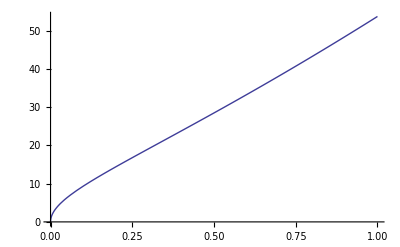

```mathematica
(*L[h_,d_]:=Sqrt[(a h^-1-Bo h^3+δ h^3 (Bi h+K1)^-3+m h^2 (Bi h+K1)^-2)/(2 (h^3))]/.{Bo-> 0, δ-> 3 k ΔT ν/(D1 σ L1 d), ϵ-> 3 k ΔT ν/(σ L1 d), m->0.109, a->0};*)
d=1*10^-3;
Plot[
2π/Sqrt[(a h^-1-Bo h^3+δ h^3 (Bi h+K1)^-3+m h^2 (Bi h+K1)^-2)/(2 (h^3))]/.{Bo-> 0, δ-> 3 k ΔT ν/(D1 σ L1 d), ϵ-> 3 k ΔT ν/(σ L1 d), m->0.109, a->0},
{h,0.000001, 1}
]
```